# Symbolic Magnus Expansion

## With PrinLieCalc 1.0

Renan Cabrera and Herschel Rabitz

Chemistry Department, Princeton University

## Initialization

```mathematica
Needs["PrinLieCalc`PrinLieCalc`"]
```

```mathematica
SetOperator[{H,H0,μ,A,B,Ω,Z,W,P,X,Y}]
```

```mathematica
SetDipoleList[{μ}]
```

Setting the format display of the time variable

```mathematica
MakeBoxes[t[n_],form:StandardForm|TraditionalForm]:=InterpretationBox[#1,#2,Editable->False]&@@{ SubscriptBox[MakeBoxes[t,form],MakeBoxes[n,form]] ,t[n]}
```

Setting the display of the Hamiltonian H0 with subscripts

```mathematica
MakeBoxes[H0,form:StandardForm|TraditionalForm]:=InterpretationBox[#1,#2,Editable->False]&@@{ SubscriptBox[MakeBoxes[H,form],MakeBoxes[0,form]] ,H0}
```

Setting the display of the frequency operator superscripts

```mathematica
MakeBoxes[ Ω[n_?(#=!=t&&#=!=T&)],form:StandardForm|TraditionalForm]:=InterpretationBox[#1,#2,Editable->False]&@@{ SubscriptBox[MakeBoxes[Ω,form],MakeBoxes[n,form]] ,Ω[n]}
```

```mathematica
MakeBoxes[ P[n_],form:StandardForm|TraditionalForm]:=InterpretationBox[#1,#2,Editable->False]&@@{ SubscriptBox[MakeBoxes[P,form],MakeBoxes[n,form]] ,P[n]}
```

```mathematica
MakeBoxes[ W[n_],form:StandardForm|TraditionalForm]:=InterpretationBox[#1,#2,Editable->False]&@@{ SubscriptBox[MakeBoxes[W,form],MakeBoxes[n,form]] ,W[n]}
```

```mathematica
MakeBoxes[ Z[n_],form:StandardForm|TraditionalForm]:=InterpretationBox[#1,#2,Editable->False]&@@{ SubscriptBox[MakeBoxes[Z,form],MakeBoxes[n,form]] ,Z[n]}
```

Setting the color of some variables

```mathematica
Format[Ω]=Style["Ω",Red];
```

```mathematica
Format[A]=Style["A",Blue];
```

```mathematica
Format[H]=Style["H",Blue];
```

```mathematica
Format[W]=Style["W",Darker[Green]];
```

```mathematica
Format[P]=Style["P",Darker[Green]];
```

```mathematica
Format[μ]=Style["μ",Red];
```

## Introduction

The Magnus expansion [1, 2] is inspired as a solution of the following linear differential equation of operators

Y'(t)=A(t)Y(t)

Y(0)=1

where 1 is the identity operator.

The first key ingredient is the following change of variable

Y(t) = ⅇ^(Ω(t))

The differential equation for Ω(t) can be  written as a series of nested commutators of  Ω(t) and A through the operator adjoint operator ad_Ω^n

(d Ω(t))/(d t)= ∑_(n=0)^∞ B_n/n ad_Ω^n A

where B_n are the Bernoulli numbers. Truncated expressions of this differential equation can be obtained with the function dΩ

```mathematica
Ω'[t]==dΩ[Ω,4,A]
```

Ω'[t]==A-(ad_Ω A)/2+1/12 (ad_Ω ad_Ω A)-1/720 (ad_Ω ad_Ω ad_Ω ad_Ω A)

This truncated expression can be written in terms of the more familiar commutators with the function adToCommutator

```mathematica
Ω'[t]==dΩ[Ω,4,A]//adToCommutator
```

Ω'[t]==A-1/2 ([Ω,A])+1/12 ([Ω,[Ω,A]])-1/720 ([Ω,[Ω,[Ω,[Ω,A]]]])

## Solving the differential equation

### Direct recursive integration

The differential equation (4) can be solved by expanding Ω(t) as a perturbative series

Ω(t)= ϵ Ω_1(t)+ ϵ^2 Ω_2(t)+ϵ^3 Ω_3(t)+...

and the differential equation (1) is decomposed in a system of infinite equations. The function MagnusPerturbativeTerms can be used to obtain a truncated system of equation as follows

Note.- The convergence of the series requires the following quite restrictive condition [3]

∫_0^t |A(t)|ⅆt< 1.086

The function MagnusPerturbativeTerms can be used to obtain a truncated system of equation as follows

```mathematica
MapThread[Equal,{Table[Ω[k]',{k,1,3}],MagnusPerturbativeTerms[Ω,2,A]}]//TableForm
```

(Ω_1)'==A
(Ω_2)'==-1/2 ([Ω_1,A])
(Ω_3)'==1/12 ([Ω_1,[Ω_1,A]])-1/2 ([Ω_2,A])

These differential equation can be solved recursively. This is implemented in the function MagnusSeries, which returns an approximation up to a certain truncation order as follows

```mathematica
Ω[t]==MagnusSeries[t,T,3,A]
```

Ω[t]==∫_0^T A[t_1]ⅆt_1-1/2 ∫_0^T [∫_0^t_2 A[t_1]ⅆt_1,A[t_2]]ⅆt_2+1/12 ∫_0^T [∫_0^t_3 A[t_1]ⅆt_1,[∫_0^t_3 A[t_1]ⅆt_1,A[t_3]]]ⅆt_3+1/4 ∫_0^T [∫_0^t_3 [∫_0^t_2 A[t_1]ⅆt_1,A[t_2]]ⅆt_2,A[t_3]]ⅆt_3

For practical purposes there are two variants that return a list and a set of rules

```mathematica
MagnusSeriesList[t,T,3,A]//TableForm
```

∫_0^T A[t_1]ⅆt_1
-1/2 ∫_0^T [∫_0^t_2 A[t_1]ⅆt_1,A[t_2]]ⅆt_2
1/12 ∫_0^T [∫_0^t_3 A[t_1]ⅆt_1,[∫_0^t_3 A[t_1]ⅆt_1,A[t_3]]]ⅆt_3+1/4 ∫_0^T [∫_0^t_3 [∫_0^t_2 A[t_1]ⅆt_1,A[t_2]]ⅆt_2,A[t_3]]ⅆt_3

```mathematica
MagnusSeriesRules[Ω,t,T,3,A]//TableForm
```

Ω_1→∫_0^T A[t_1]ⅆt_1
Ω_2→-1/2 ∫_0^T [∫_0^t_2 A[t_1]ⅆt_1,A[t_2]]ⅆt_2
Ω_3→1/12 ∫_0^T [∫_0^t_3 A[t_1]ⅆt_1,[∫_0^t_3 A[t_1]ⅆt_1,A[t_3]]]ⅆt_3+1/4 ∫_0^T [∫_0^t_3 [∫_0^t_2 A[t_1]ⅆt_1,A[t_2]]ⅆt_2,A[t_3]]ⅆt_3

### Combinatorial Graphs

The rooted trees expressions and their graphs are generated with the functions RootedTreeExpression and RootedTreeGraph. For example, the rooted tree of second order is

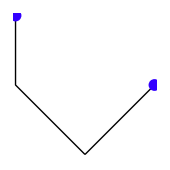

```mathematica
RootedTreeExpression[2];
Map[RootedTreeGraph[#,ImageSize->{170,170}]&,%]
```

third order

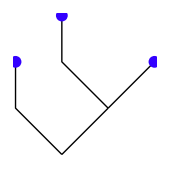
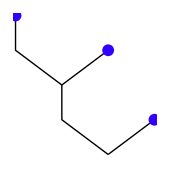

```mathematica
RootedTreeExpression[3];
Map[RootedTreeGraph[#,ImageSize->{170,170}]&,%]
```

fourth order

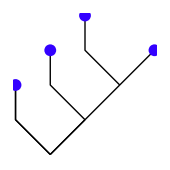
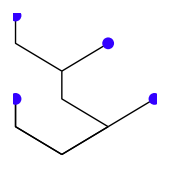
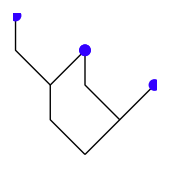
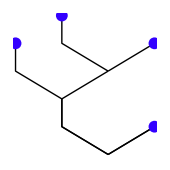
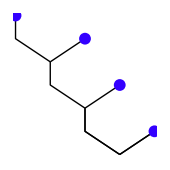

```mathematica
RootedTreeExpression[4];
Map[RootedTreeGraph[#,ImageSize->{170,170}]&,%]
```

Each rooted tree represents a term in the Magnus expansion [4, 5]. All the information of each term is encoded in the rooted tree including the coefficients. The rooted tree of second order along with the corresponding term is for example

{RootedTree[1,2]}

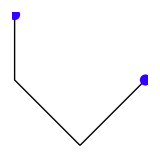
{{-Graphics-,-1/2 ∫_0^T [∫_0^t_2 A[t_1]ⅆt_1,A[t_2]]ⅆt_2}}

```mathematica
RootedTreeExpression[2]
{RootedTreeGraph/@%,
RootedTreeToIntegral[A,t,T]/@%}//Transpose
```

The coefficients are calculated by counting the number of right diagonal branches and how long they stretch according to the following formula

Coefficient = ϕ(Length_1)^Number_1 ϕ(Length_2)^Number_2...

The function ϕ is given by

```mathematica
RootedTreeCoefficientFunction[L_]=BernoulliB[L]/L!
```

BernoulliB[L]/(L!)

Fox example, the rooted trees of third order are

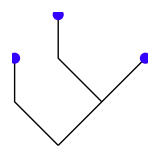
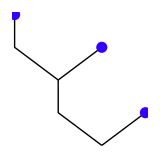
{{-Graphics-,1/12 ∫_0^T [∫_0^t_3 A[t_2]ⅆt_2,[∫_0^t_3 A[t_2]ⅆt_2,A[t_3]]]ⅆt_3},{-Graphics-,1/4 ∫_0^T [∫_0^t_3 [∫_0^t_2 A[t_1]ⅆt_1,A[t_2]]ⅆt_2,A[t_3]]ⅆt_3}}

```mathematica
RootedTreeExpression[3];
{RootedTreeGraph/@%,
RootedTreeToIntegral[A,t,T]/@%}//Transpose
```

The following tree has one right diagonal branch of length 2 and zero diagonal branches of length 1

```mathematica
RootedTreeGraph[Part[RootedTreeExpression[3],1]]
```

-Graphics-

The corresponding coefficient is calculated as

```mathematica
RootedTreeCoefficientFunction[1]^0*RootedTreeCoefficientFunction[2]^1
```

1/12

The following tree has two right diagonal branches of length 1

```mathematica
RootedTreeGraph[Part[RootedTreeExpression[3],2]]
```

-Graphics-

so, the corresponding coefficient is

```mathematica
RootedTreeCoefficientFunction[1]^2*RootedTreeCoefficientFunction[2]^0
```

1/4

This method is implemented in the functions MagnusSeries, MagnusSeriesList, and MagnusSeriesRules and executed with the option Method → "RootedTree" as follows

```mathematica
MagnusSeries[t,T,3,A,Method->"RootedTree"]
```

∫_0^T A[t_1]ⅆt_1-1/2 ∫_0^T [∫_0^t_2 A[t_1]ⅆt_1,A[t_2]]ⅆt_2+1/12 ∫_0^T [∫_0^t_3 A[t_2]ⅆt_2,[∫_0^t_3 A[t_2]ⅆt_2,A[t_3]]]ⅆt_3+1/4 ∫_0^T [∫_0^t_3 [∫_0^t_2 A[t_1]ⅆt_1,A[t_2]]ⅆt_2,A[t_3]]ⅆt_3

```mathematica
MagnusSeriesRules[Ω,t,T,3,A,Method->"RootedTree"]//TableForm
```

Ω_1→∫_0^T A[t_1]ⅆt_1
Ω_2→-1/2 ∫_0^T [∫_0^t_2 A[t_1]ⅆt_1,A[t_2]]ⅆt_2
Ω_3→1/12 ∫_0^T [∫_0^t_3 A[t_2]ⅆt_2,[∫_0^t_3 A[t_2]ⅆt_2,A[t_3]]]ⅆt_3+1/4 ∫_0^T [∫_0^t_3 [∫_0^t_2 A[t_1]ⅆt_1,A[t_2]]ⅆt_2,A[t_3]]ⅆt_3

Note.- This method may return expressions with different labeling compared with the direct integration method.

### Orderder Integrals of the Dyson series

The solution of the differential equation under consideration (1) can be expressed in terms of the Dyson series, which is a series made of ordered integrals

Y(t) = T ⅇ^(∫_0^t A(t_1)ⅆ t_1)=1+∫_0^t A(t_1)ⅆ t_1+∫_0^t ∫_0^t_2 A(t_2)A(t_1)ⅆ t_1ⅆ t_2+...

The ordered integrals that participate in the Dyson series can be generated with the function OrderedIntegralRules as

```mathematica
OrderedIntegralRules[4,P,t,T,A]//TableForm
```

P_1→∫_0^T A[t_1]ⅆt_1
P_2→∫_0^T A[t_2].∫_0^t_2 A[t_1]ⅆt_1ⅆt_2
P_3→∫_0^T A[t_3].∫_0^t_3 A[t_2].∫_0^t_2 A[t_1]ⅆt_1ⅆt_2ⅆt_3
P_4→∫_0^T A[t_4].∫_0^t_4 A[t_3].∫_0^t_3 A[t_2].∫_0^t_2 A[t_1]ⅆt_1ⅆt_2ⅆt_3ⅆt_4

The Magnus expansion can be written in terms of the ordered integrals [2,7] as

```mathematica
MagnusOrderedIntegralRules[4,Ω,P]//TableForm
```

Ω_1→P_1
Ω_2→-1/2 P_1.P_1+P_2
Ω_3→-1/2 P_1.P_2-(P_2.P_1)/2+1/3 P_1.P_1.P_1+P_3
Ω_4→-1/2 P_1.P_3-(P_2.P_2)/2-(P_3.P_1)/2+1/3 P_1.P_1.P_2+1/3 P_1.P_2.P_1+1/3 P_2.P_1.P_1-1/4 P_1.P_1.P_1.P_1+P_4

Conversely, the ordered integrals can be expressed in terms of the terms of the Magnus expansion as

```mathematica
MagnusOrderedIntegralInvertedRules[4,P,Ω]//Expand//TableForm
```

P_1→Ω_1
P_2→(Ω_1.Ω_1)/2+Ω_2
P_3→(Ω_1.Ω_2)/2+(Ω_2.Ω_1)/2+1/6 Ω_1.Ω_1.Ω_1+Ω_3
P_4→(Ω_1.Ω_3)/2+(Ω_2.Ω_2)/2+(Ω_3.Ω_1)/2+1/6 Ω_1.Ω_1.Ω_2+1/6 Ω_1.Ω_2.Ω_1+1/6 Ω_2.Ω_1.Ω_1+1/24 Ω_1.Ω_1.Ω_1.Ω_1+Ω_4

which can be used to express the Dyson series in terms of nested commutators.

The Magnus expansion can be expressed directly in terms of the product of ordered integrals with the option 
Method → "OrderedIntegral" as

```mathematica
MagnusSeriesRules[Ω,t,T,3,A,Method->"OrderedIntegral"]//TableForm
```

Ω_1→∫_0^T A[t_1]ⅆt_1
Ω_2→-1/2 (∫_0^T A[t_1]ⅆt_1).∫_0^T A[t_1]ⅆt_1+∫_0^T A[t_2].∫_0^t_2 A[t_1]ⅆt_1ⅆt_2
Ω_3→-1/2 (∫_0^T A[t_1]ⅆt_1).∫_0^T A[t_2].∫_0^t_2 A[t_1]ⅆt_1ⅆt_2-1/2 (∫_0^T A[t_2].∫_0^t_2 A[t_1]ⅆt_1ⅆt_2).∫_0^T A[t_1]ⅆt_1+1/3 (∫_0^T A[t_1]ⅆt_1).(∫_0^T A[t_1]ⅆt_1).∫_0^T A[t_1]ⅆt_1+∫_0^T A[t_3].∫_0^t_3 A[t_2].∫_0^t_2 A[t_1]ⅆt_1ⅆt_2ⅆt_3

SO, THERE ARE THREE DIFFERENT METHODS TO GENERATE THE MAGNUS EXPANSION!

## Testing consistency

### Direct recursive integration Vs combinatorial graphs

One of the reasons to develop different methods to generate the Magnus series is to have the means to validate them by demanding consistency with each other. The Magnus series by direct recursive integration and rooted trees is calculated as

```mathematica
mgRootedTree=(MagnusSeries[t,T,3,A,Method->"RootedTree"]/.{ A[u_]-> I*(H0- μ*Sin[u])})/.HoldIntegrate-> Integrate//Simplify;
```

```mathematica
mgDirect=(MagnusSeries[t,T,3,A]/.{ A[u_]-> I*(H0- μ*Sin[u])})/.HoldIntegrate-> Integrate//Simplify;
```

giving exactly the same result as we can see from the zero subtraction

```mathematica
mgDirect-mgRootedTree//Simplify
```

0

### Direct recursive integration Vs ordered integrals

The equivalence between the rooted trees and the ordered integrals is also verified

```mathematica
mgRootedTree2=Expand@FullSimplify[FullDotSimplify@ExpandCommutator[MagnusSeries[t,T,3,A,Method->"RootedTree"]/.{ A[u_]-> I*(H0- μ*Sin[u])}]/.HoldIntegrate->Integrate];
```

```mathematica
mgOintegrals=Expand@FullSimplify[FullDotSimplify@ExpandCommutator[MagnusSeries[t,T,3,A,Method->"OrderedIntegral"]/.{ A[u_]-> I*(H0- μ*Sin[u])}]/.HoldIntegrate->Integrate];
```

```mathematica
mgRootedTree2-mgOintegrals//Simplify
```

0

### The Baker-Campbell-Hausdorff (BCH) expansion from the Magnus expansion

The Baker–Campbell–Hausdorff expansion defines the composition of the product of the exponential of two operators  as

ⅇ^A ⅇ^B= ⅇ^(Z_1+Z_2+Z_3+...)

or in terms of the matrix Log

MatrixLog(ⅇ^A ⅇ^B)= (Z_1+Z_2+Z_3+...)^.

The BCH expansion is calculated by default using the Wilcox method [9], but it also can be calculated from the Magnus series by choosing a piecewise function for A(t) as shown in [2]. The BCH expansion with the Wilcox method is implemented in the function BCHExpansionList

```mathematica
(bch1=BCHExpansionList[5,{X,Y}]//ExpandCommutator//FullDotSimplify)//TableForm
```

X+Y
1/2 (X.Y-Y.X)
1/12 (X.X.Y-2 X.Y.X+Y.X.X)+1/12 (X.Y.Y-2 Y.X.Y+Y.Y.X)
1/24 (X.X.Y.Y-2 X.Y.X.Y+2 Y.X.Y.X-Y.Y.X.X)
1/720 (-X.X.X.X.Y+4 X.X.X.Y.X-6 X.X.Y.X.X+4 X.Y.X.X.X-Y.X.X.X.X)+1/120 (-X.X.Y.X.Y+X.X.Y.Y.X+3 X.Y.X.X.Y-4 X.Y.X.Y.X+X.Y.Y.X.X-2 Y.X.X.X.Y+3 Y.X.X.Y.X-Y.X.Y.X.X)+1/48 (X.X.Y.X.Y-X.X.Y.Y.X-3 X.Y.X.X.Y+4 X.Y.X.Y.X-X.Y.Y.X.X+2 Y.X.X.X.Y-3 Y.X.X.Y.X+Y.X.Y.X.X)+1/240 (-X.X.X.Y.Y+2 X.X.Y.X.Y+X.X.Y.Y.X-4 X.Y.X.Y.X+X.Y.Y.X.X+2 Y.X.Y.X.X-Y.Y.X.X.X)+7/720 (X.X.X.Y.Y-3 X.X.Y.X.Y+3 X.Y.X.X.Y-2 Y.X.X.X.Y+3 Y.X.X.Y.X-3 Y.X.Y.X.X+Y.Y.X.X.X)+1/240 (-X.Y.X.Y.Y+3 X.Y.Y.X.Y-2 X.Y.Y.Y.X+Y.X.X.Y.Y-4 Y.X.Y.X.Y+3 Y.X.Y.Y.X+Y.Y.X.X.Y-Y.Y.X.Y.X)+1/120 (X.Y.X.Y.Y-3 X.Y.Y.X.Y+2 X.Y.Y.Y.X-Y.X.X.Y.Y+4 Y.X.Y.X.Y-3 Y.X.Y.Y.X-Y.Y.X.X.Y+Y.Y.X.Y.X)+1/720 (X.X.Y.Y.Y-3 X.Y.X.Y.Y+3 X.Y.Y.X.Y-2 X.Y.Y.Y.X+3 Y.X.Y.Y.X-3 Y.Y.X.Y.X+Y.Y.Y.X.X)+1/240 (X.X.Y.Y.Y-2 X.Y.X.Y.Y-Y.X.X.Y.Y+4 Y.X.Y.X.Y-Y.Y.X.X.Y-2 Y.Y.X.Y.X+Y.Y.Y.X.X)+1/720 (-X.Y.Y.Y.Y+4 Y.X.Y.Y.Y-6 Y.Y.X.Y.Y+4 Y.Y.Y.X.Y-Y.Y.Y.Y.X)

The BCH expansion, through the Magnus expansion is obtained with the option  Method → "Magnus"

```mathematica
(bch2=BCHExpansionList[5,{X,Y},Method->"Magnus"]//ExpandCommutator//FullDotSimplify)//TableForm
```

X+Y
1/2 (X.Y-Y.X)
1/12 (X.X.Y-2 X.Y.X+Y.X.X)+1/12 (X.Y.Y-2 Y.X.Y+Y.Y.X)
1/24 (X.X.Y.Y-2 X.Y.X.Y+2 Y.X.Y.X-Y.Y.X.X)
1/720 (-X.X.X.X.Y+4 X.X.X.Y.X-6 X.X.Y.X.X+4 X.Y.X.X.X-Y.X.X.X.X)+1/432 (-X.X.Y.X.Y+X.X.Y.Y.X+3 X.Y.X.X.Y-4 X.Y.X.Y.X+X.Y.Y.X.X-2 Y.X.X.X.Y+3 Y.X.X.Y.X-Y.X.Y.X.X)+1/144 (X.X.Y.X.Y-X.X.Y.Y.X-3 X.Y.X.X.Y+4 X.Y.X.Y.X-X.Y.Y.X.X+2 Y.X.X.X.Y-3 Y.X.X.Y.X+Y.X.Y.X.X)+1/540 (X.X.X.Y.Y-3 X.X.Y.X.Y+3 X.Y.X.X.Y-2 Y.X.X.X.Y+3 Y.X.X.Y.X-3 Y.X.Y.X.X+Y.Y.X.X.X)+1/270 (X.X.X.Y.Y-2 X.X.Y.X.Y-X.X.Y.Y.X+4 X.Y.X.Y.X-X.Y.Y.X.X-2 Y.X.Y.X.X+Y.Y.X.X.X)+1/288 (X.Y.X.Y.Y-3 X.Y.Y.X.Y+2 X.Y.Y.Y.X-Y.X.X.Y.Y+4 Y.X.Y.X.Y-3 Y.X.Y.Y.X-Y.Y.X.X.Y+Y.Y.X.Y.X)+(X.X.Y.Y.Y-3 X.Y.X.Y.Y+3 X.Y.Y.X.Y-2 X.Y.Y.Y.X+3 Y.X.Y.Y.X-3 Y.Y.X.Y.X+Y.Y.Y.X.X)/1440+(7 (X.X.Y.Y.Y-2 X.Y.X.Y.Y-Y.X.X.Y.Y+4 Y.X.Y.X.Y-Y.Y.X.X.Y-2 Y.Y.X.Y.X+Y.Y.Y.X.X))/1440+1/720 (-X.Y.Y.Y.Y+4 Y.X.Y.Y.Y-6 Y.Y.X.Y.Y+4 Y.Y.Y.X.Y-Y.Y.Y.Y.X)

and we can verify that they give the same answer

```mathematica
bch1-bch2//Simplify
```

{0,0,0,0,0}

## The quantum time-evolution operator for dipole interactions

### Introduction

The interaction is expressed in terms of the following Hamiltonian

H(t) = H_0- μ ε(t)

such that

A(t)= -ⅈ H(t)

The truncated Magnus expansion up to third order is calculated as

```mathematica
dipoleInteractionRule = { A[u_]-> -I*(H0- μ*ε[u])}
```

{A[u_]→-ⅈ (H_0-μ ε[u])}

```mathematica
MagnusSeries[t,T,3,A];
%/.dipoleInteractionRule
```

-ⅈ (H_0 T-μ ∫_0^T ε[t_1]ⅆt_1)+1/2 (-([μ,H_0]) ∫_0^T ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2-([H_0,μ]) ∫_0^T t_2 ε[t_2]ⅆt_2)-1/4 ⅈ (([[μ,H_0],H_0]) ∫_0^T ∫_0^t_3 ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2ⅆt_3+([[H_0,μ],H_0]) ∫_0^T ∫_0^t_3 t_2 ε[t_2]ⅆt_2ⅆt_3-([[μ,H_0],μ]) ∫_0^T (∫_0^t_3 ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2) ε[t_3]ⅆt_3-([[H_0,μ],μ]) ∫_0^T (∫_0^t_3 t_2 ε[t_2]ⅆt_2) ε[t_3]ⅆt_3)-1/12 ⅈ (-([μ,[μ,H_0]]) ∫_0^T (∫_0^t_3 ε[t_1]ⅆt_1)^2 ⅆt_3+([H_0,[μ,H_0]]) ∫_0^T (∫_0^t_3 ε[t_1]ⅆt_1) t_3ⅆt_3-([μ,[H_0,μ]]) ∫_0^T (∫_0^t_3 ε[t_1]ⅆt_1) t_3 ε[t_3]ⅆt_3+([H_0,[H_0,μ]]) ∫_0^T (t_3)^2 ε[t_3]ⅆt_3)

which can be simplified by collecting independent commutators  with the function ArrangeCommutatorArgLeft as

```mathematica
MagnusSeriesList[t,T,3,A]/.dipoleInteractionRule;
(magnusList1=%//ArrangeCommutatorArgLeft[μ])//TableForm
```

-ⅈ H_0 T+ⅈ μ ∫_0^T ε[t_1]ⅆt_1
([μ,H_0]) (-1/2 ∫_0^T ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2+1/2 ∫_0^T t_2 ε[t_2]ⅆt_2)
([μ,[μ,H_0]]) (1/12 ⅈ ∫_0^T (∫_0^t_3 ε[t_1]ⅆt_1)^2 ⅆt_3-1/4 ⅈ ∫_0^T (∫_0^t_3 ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2) ε[t_3]ⅆt_3+1/4 ⅈ ∫_0^T (∫_0^t_3 t_2 ε[t_2]ⅆt_2) ε[t_3]ⅆt_3-1/12 ⅈ ∫_0^T (∫_0^t_3 ε[t_1]ⅆt_1) t_3 ε[t_3]ⅆt_3)+([[μ,H_0],H_0]) (-1/4 ⅈ ∫_0^T ∫_0^t_3 ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2ⅆt_3+1/4 ⅈ ∫_0^T ∫_0^t_3 t_2 ε[t_2]ⅆt_2ⅆt_3+1/12 ⅈ ∫_0^T (∫_0^t_3 ε[t_1]ⅆt_1) t_3ⅆt_3-1/12 ⅈ ∫_0^T (t_3)^2 ε[t_3]ⅆt_3)

The evaluation of the integrals can be carried out giving a certain field.

```mathematica
field[t_] = (Sin[t]+Sin[4t]^3);
```

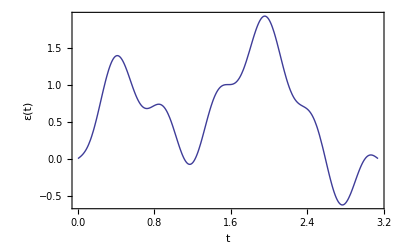

```mathematica
Plot[
field[t],{t,0,Pi},
BaseStyle->{FontSize->16},Frame->True, FrameLabel->{"t","ε(t)"},RotateLabel->False]
```

The following set of Hamiltonians are set

```mathematica
HamiltoniansRule = {
H0-> ({{0.3, 0., 0.}, {0., 0.8, 0.}, {0., 0., 0.}})/10,
μ->  ({{0.5, 1., 0.5}, {1., 0.64, 1.}, {0.5, 1., 0.02}})/100
};
```

The convergence condition is met

```mathematica
((A[t]/.dipoleInteractionRule)/.HamiltoniansRule)/.ε-> field;
Sqrt[Tr[%.MForceHermitianConjugation[%]]];
NIntegrate[ %,{t,0,Pi}]
```

0.260354

### Exporting C++ code

#### Calculating the truncated expansion

In order to perform efficient evaluation we have the option to generate standard C++ code with the use of the C++ library for linear algebra Armadillo [6]. The code was tested with the C++ compiler in a Linux system.

```mathematica
MagnusSeries[t,T,3,A]/.{ A[u_]-> I*(H0- μ*ε[u])};
(magnus1=%//ArrangeCommutatorArgLeft[μ]);
```

The C++ code generator function is

```mathematica
?CCodeGenerationArmadillo
```

CCodeGeneration[{ε_,F_},{μ_,M_},{f_,g_}][mags_], generates a list of two elements: 

1) The header functions

2) The function definitions

Assuming that ε is the field to be replaced by the array F and μ is the dipole to be replaced by the array M. 

f and g are the name of the internal functions needed to make the the C code.

This function is tailored to use the Armadillo c++ linear algebra package http://arma.sourceforge.net/

```mathematica
magnusArmadillo=CCodeGenerationArmadillo[{ε,F},{μ,M},{f,g}][{magnus1}];
```

An extraction of the generated container file is

```mathematica
Part[magnusArmadillo, 2]//Short[#,7]&
```

#include"magnus.h"
#include "/home/cabrer7/Documents/source/C/armadillo/armadillo-0.6.8/include/armadillo"

#include<math.h>
#include<complex.h>
extern double*F;

cx_mat Commutator(cx_mat A, cx_mat B){ return A*B - B*A;}

double pow(int A, int B){ re…t);
}
double g$2055( int t){
return PrinLieCalc_PrinLieCalc_Private_sum(&f$2037,0,t);
}
double g$2061( int t){
return PrinLieCalc_PrinLieCalc_Private_sum(&f$2057,0,t);
}
double g$2063( int t){
return PrinLieCalc_PrinLieCalc_Private_sum(&f$2059,0,t);
}

The header file is saved as

```mathematica
Export["/home/cabrer7/Documents/source/mathematica/magnus/cIMUC/_magnus.h", Part[magnusArmadillo, 1], "Text"];
```

The function container is saved as

```mathematica
Export["/home/cabrer7/Documents/source/mathematica/magnus/cIMUC/_magnus.cc", Part[magnusArmadillo,2], "Text"];
```

The code requires some editing in order to provide the path of the armadillo library, the name of the header and container files where the code was written. The function MagnusSeries located in the container file must be eventually edited in order to account for the name of the free evolution Hamiltonian and dipole operator.

Additionally, the evaluation of this C++ code requires a main function that defines the corresponding numerical field as well as the Hamiltinonians.

Note.- The source code is slightly different each time is generated, so, the header and container files are intended to be used always together in combination. In other words, the header file from one generation is not going to work with the container file of another generation.

#### Calculating separated parts

The sequence of terms in the Magnus expansion can be generated as a List

```mathematica
magnusList=Rest@Sort[
List@@ArrangeCommutatorArgLeft[μ][MagnusSeries[t,T,4,A]/.{ A[u_]-> I*(H0- μ*ε[u])}]
,LeafCount[#1]<LeafCount[#2]&];
%//TableForm
```

-ⅈ μ ∫_0^T ε[t_1]ⅆt_1
([μ,H_0]) (-1/2 ∫_0^T ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2+1/2 ∫_0^T t_2 ε[t_2]ⅆt_2)
([[μ,H_0],H_0]) (1/4 ⅈ ∫_0^T ∫_0^t_3 ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2ⅆt_3-1/4 ⅈ ∫_0^T ∫_0^t_3 t_2 ε[t_2]ⅆt_2ⅆt_3-1/12 ⅈ ∫_0^T (∫_0^t_3 ε[t_1]ⅆt_1) t_3ⅆt_3+1/12 ⅈ ∫_0^T (t_3)^2 ε[t_3]ⅆt_3)
([μ,[μ,H_0]]) (-1/12 ⅈ ∫_0^T (∫_0^t_3 ε[t_1]ⅆt_1)^2 ⅆt_3+1/4 ⅈ ∫_0^T (∫_0^t_3 ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2) ε[t_3]ⅆt_3-1/4 ⅈ ∫_0^T (∫_0^t_3 t_2 ε[t_2]ⅆt_2) ε[t_3]ⅆt_3+1/12 ⅈ ∫_0^T (∫_0^t_3 ε[t_1]ⅆt_1) t_3 ε[t_3]ⅆt_3)
([[[μ,H_0],H_0],H_0]) (1/8 ∫_0^T ∫_0^t_4 ∫_0^t_3 ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2ⅆt_3ⅆt_4-1/8 ∫_0^T ∫_0^t_4 ∫_0^t_3 t_2 ε[t_2]ⅆt_2ⅆt_3ⅆt_4-1/24 ∫_0^T ∫_0^t_4 (∫_0^t_3 ε[t_1]ⅆt_1) t_3ⅆt_3ⅆt_4+1/24 ∫_0^T ∫_0^t_4 (t_3)^2 ε[t_3]ⅆt_3ⅆt_4-1/24 ∫_0^T (∫_0^t_4 ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2) t_4ⅆt_4+1/24 ∫_0^T (∫_0^t_4 t_2 ε[t_2]ⅆt_2) t_4ⅆt_4)
([[μ,[μ,H_0]],H_0]) (-1/24 ∫_0^T ∫_0^t_4 (∫_0^t_3 ε[t_1]ⅆt_1)^2 ⅆt_3ⅆt_4+1/8 ∫_0^T ∫_0^t_4 (∫_0^t_3 ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2) ε[t_3]ⅆt_3ⅆt_4-1/8 ∫_0^T ∫_0^t_4 (∫_0^t_3 t_2 ε[t_2]ⅆt_2) ε[t_3]ⅆt_3ⅆt_4+1/24 ∫_0^T ∫_0^t_4 (∫_0^t_3 ε[t_1]ⅆt_1) t_3 ε[t_3]ⅆt_3ⅆt_4-1/24 ∫_0^T (∫_0^t_4 ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2) t_4 ε[t_4]ⅆt_4+1/24 ∫_0^T (∫_0^t_4 t_2 ε[t_2]ⅆt_2) t_4 ε[t_4]ⅆt_4)
([μ,[[μ,H_0],H_0]]) (-1/24 ∫_0^T (∫_0^t_4 ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2) ∫_0^t_4 ε[t_1]ⅆt_1ⅆt_4+1/24 ∫_0^T (∫_0^t_4 ε[t_1]ⅆt_1) ∫_0^t_4 t_2 ε[t_2]ⅆt_2ⅆt_4+1/8 ∫_0^T (∫_0^t_4 ∫_0^t_3 ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2ⅆt_3) ε[t_4]ⅆt_4-1/8 ∫_0^T (∫_0^t_4 ∫_0^t_3 t_2 ε[t_2]ⅆt_2ⅆt_3) ε[t_4]ⅆt_4-1/24 ∫_0^T (∫_0^t_4 (∫_0^t_3 ε[t_1]ⅆt_1) t_3ⅆt_3) ε[t_4]ⅆt_4+1/24 ∫_0^T (∫_0^t_4 (t_3)^2 ε[t_3]ⅆt_3) ε[t_4]ⅆt_4)
([μ,[μ,[μ,H_0]]]) (-1/24 ∫_0^T (∫_0^t_4 (∫_0^t_3 ε[t_1]ⅆt_1)^2 ⅆt_3) ε[t_4]ⅆt_4-1/24 ∫_0^T (∫_0^t_4 ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2) (∫_0^t_4 ε[t_1]ⅆt_1) ε[t_4]ⅆt_4+1/24 ∫_0^T (∫_0^t_4 ε[t_1]ⅆt_1) (∫_0^t_4 t_2 ε[t_2]ⅆt_2) ε[t_4]ⅆt_4+1/8 ∫_0^T (∫_0^t_4 (∫_0^t_3 ∫_0^t_2 ε[t_1]ⅆt_1ⅆt_2) ε[t_3]ⅆt_3) ε[t_4]ⅆt_4-1/8 ∫_0^T (∫_0^t_4 (∫_0^t_3 t_2 ε[t_2]ⅆt_2) ε[t_3]ⅆt_3) ε[t_4]ⅆt_4+1/24 ∫_0^T (∫_0^t_4 (∫_0^t_3 ε[t_1]ⅆt_1) t_3 ε[t_3]ⅆt_3) ε[t_4]ⅆt_4)

, where we excluded the first trivial term that does not involve any integral.

The function CCodeGenerationArmadilloList can be used to generate the C++ code for each of the terms

```mathematica
magnusArmadilloList=CCodeGenerationArmadilloList[{ε,F},{μ,M},{f,g}]@magnusList;
```

```mathematica
Export["/home/cabrer7/Documents/source/mathematica/magnus/cIMUC/_magnus.h", Part[magnusArmadilloList, 1], "Text"];
```

```mathematica
Export["/home/cabrer7/Documents/source/mathematica/magnus/cIMUC/_magnus.cc", Part[magnusArmadilloList,2], "Text"];
```

```mathematica
fileIm2=ReadList["/home/cabrer7/Documents/source/mathematica/magnus/cIMUC/output/ImaginaryOutput2.txt",Number,RecordLists->True];
```

```mathematica
Take[fileIm2,3]/Take[fileIm2,{4,6}]
```

{{0.437957,0.437957,0.437957},{0.437957,0.437957,0.437957},{0.437957,0.437957,0.437957}}

## Dyson/Magnus a comparative analysis of robust implementation

```mathematica
MagnusOrderedIntegralInvertedRules[4,P,Ω]//Expand//TableForm
```

P_1→Ω_1
P_2→(Ω_1.Ω_1)/2+Ω_2
P_3→(Ω_1.Ω_2)/2+(Ω_2.Ω_1)/2+1/6 Ω_1.Ω_1.Ω_1+Ω_3
P_4→(Ω_1.Ω_3)/2+(Ω_2.Ω_2)/2+(Ω_3.Ω_1)/2+1/6 Ω_1.Ω_1.Ω_2+1/6 Ω_1.Ω_2.Ω_1+1/6 Ω_2.Ω_1.Ω_1+1/24 Ω_1.Ω_1.Ω_1.Ω_1+Ω_4

## References

[1] W. Magnus, "On the exponential solution of differential equations for a linear operator", Communications on pure and applied mathematics, vol 7, 4, 1954

[2] S. Blanes, F.Casas, J.A.Oteo, J. Ros,  "The Magnus expansion and some of its applications", Physics Reports, vol 470, 5-6, 2009  arXiv : 0810.5488 v1[math - ph] 30 Oct 2008

[3] S. Blanes, F. Casas, J.A. Oteo, and J. Ros. "Magnus and Fer expansions for
matrix differential equations: the convergence problem". J. Phys. A: Math. Gen., 22:259–268, 1998.

[4] A. Iserles and SP Nörsett, "On the solution of linear differential equations in Lie groups", Philosophical Transactions: Mathematical, Physical and Engineering Sciences, pp 983--1019, 1999

[5] A. Iserles and H.Z. Munthe-Kaas and S.P. Nörsett and A. Zanna, "Lie-group methods", Acta numerica, vol 9, pp215--365, 2001

[6] Armadillo C++ Linear Algebra Library: http://arma.sourceforge.net/

[7] R.M. Wilcox, "Exponential operators and parameter differentiation in quantum physics", Journal of Mathematical Physics, vol 8, "1967"

[8] W.R. Salzman, "An alternative to the magnus expansion in time-dependent perturbation theory", The Journal of Chemical Physics, vol 82, pp 822, 1985

## Appendix. Testing and some extra functions

### Wilcox factorization

#### Introduction

The Baker–Campbell–Hausdorff expansion defines the composition of the product of the exponential of two operators  as

ⅇ^A ⅇ^B= ⅇ^(Z_1+Z_2+Z_3+...)

or in terms of the matrix Log

MatrixLog(ⅇ^A ⅇ^B)= (Z_1+Z_2+Z_3+...)^.

The Wilcox polynomial [7,2] is defined as the n-order truncation of the following product of n exponentials

WilcoxPolynomial(n,W,ϵ) = MatrixLog(  ⅇ^(ϵ W_1)  ⅇ^(ϵ^2 W_2)... ⅇ^(ϵ^n W_n) )

The Wilcox polynomial can be used to write the Magnus expansion in terms of a product of exponentials

ⅇ^(ϵ Ω_1(t)+ ϵ^2 Ω_2(t)+...+ϵ^n Ω_n(t))=ⅇ^(ϵ W_1)  ⅇ^(ϵ^2 W_2)... ⅇ^(ϵ^n W_n)

#### BCH expansion

The function BCHExpansionRules gives a list or rules for the values of Z_k

```mathematica
(bchrule3=BCHExpansionRules[3,{A,B},Z])//TableForm
```

Z_1→A+B
Z_2→1/2 ([A,B])
Z_3→1/12 ([A,[A,B]])+1/12 ([[A,B],B])

the commutators can be expanded in terms of the product of the operators as

```mathematica
bchrule3//ExpandCommutator;
%//FullDotSimplify//Simplify//TableForm
```

Z_1→A+B
Z_2→1/2 (A.B-B.A)
Z_3→1/12 (A.A.B-2 A.B.A+A.B.B+B.A.A-2 B.A.B+B.B.A)

Another way to generate the same terms is by using the function BCHExpansionList

#### BCHExpansionList[4, {A, B}] // TableForm

A+B
1/2 ([A,B])
1/12 ([A,[A,B]])+1/12 ([[A,B],B])
1/24 ([[A,[A,B]],B])

#### Wilcox factorization

The fourth order Wilcox polynomial is calculated for example as

```mathematica
WilcoxPolynomial[4,W,ϵ]
```

1/12 ϵ^4 ([W_1,[W_1,W_2]])+1/2 ϵ^3 ([W_1,W_2])+1/2 ϵ^4 ([W_1,W_3])+ϵ W_1+ϵ^2 W_2+ϵ^3 W_3+ϵ^4 W_4

The identification of the Wilcox polynomial up to fourth order is

```mathematica
WilcoxFactorizationRules[4,{W,Ω}]//TableForm
```

W_1→Ω_1
W_2→Ω_2
W_3→-1/2 ([Ω_1,Ω_2])+Ω_3
W_4→1/6 ([Ω_1,[Ω_1,Ω_2]])-1/2 ([Ω_1,Ω_3])+Ω_4

The Wilcox terms can be put in terms of the nested integrals and in terms of the interaction Hamiltonians

```mathematica
WilcoxFactorizationRules[4,{W,Ω}];
wilcox4=%/.MagnusSeriesRules[Ω,t,T,4,A];
```

The whole expression is too large for direct display, but an extraction is

```mathematica
wilcox4/.{ A[u_]-> I*(H0- μ*ε[u])}//ArrangeCommutatorArgLeft[μ]//Short[#,10]&
```

{«1»}

### Extra functions

```mathematica
ad[A][H]
```

ad_A H

```mathematica
ad[A+Ω ][H]
```

ad_A H+ad_Ω H

```mathematica
ad[A,2][H]
```

ad_A ad_A H

The adjoint operator involving elements not listed in SetOperatorsList are automatically evaluated zero

```mathematica
ad[B][A]
```

ad_B A

The commutator obeys the same properties

```mathematica
Commutator[A,H]
```

[A,H]

```mathematica
Commutator[A,2]
```

0

```mathematica
ad[A][H]
%//adToCommutator
```

ad_A H

[A,H]

```mathematica
ad[A,2][H]
%//adToCommutator
```

ad_A ad_A H

[A,[A,H]]

We define an integration function in order to avoid interference with the standard integration function.

```mathematica
HoldIntegrate[2*A[t],{t,t[0],t[1]}]
```

2 ∫_t_0^t_1 A[t]ⅆt

The integration of expressions that do not contain the integration variable get out of the integration automatically

```mathematica
HoldIntegrate[μ*A[t],{t,t[0],t[1]}]
```

μ ∫_t_0^t_1 A[t]ⅆt

```mathematica
HoldIntegrate[ ad[H][μ]  A[t],{t,t[0],t[1]}]
```

(∫_t_0^t_1 A[t]ⅆt) (ad_H μ)

```mathematica
HoldIntegrate[a,{t,t[1],t[2]}]
```

a (-t_1+t_2)

```mathematica
HoldIntegrate[μ*A[ t[1] ],{t[1],0,t[2]}]
```

μ ∫_0^t_2 A[t_1]ⅆt_1

The truncated exponential of a scalar

```mathematica
DotExp[4][a]
DotSimplify[%]
```

1+a+a^2/2+a^3/6+a^4/24

1+a+a^2/2+a^3/6+a^4/24

The truncated exponential of an operator times a scalar

```mathematica
DotExp[4][a*A]
```

1+a A+1/2 a^2 A.A+1/6 a^3 A.A.A+1/24 a^4 A.A.A.A

```mathematica
DotExp[3][a*A+b*H]
```

1+a A+b H+1/2 (a^2 A.A+a b A.H+a b H.A+b^2 H.H)+1/6 (a^3 A.A.A+a^2 b A.A.H+a^2 b A.H.A+a b^2 A.H.H+a^2 b H.A.A+a b^2 H.A.H+a b^2 H.H.A+b^3 H.H.H)

```mathematica
DotExp[3][ϵ*Ω[1] +ϵ^2*Ω[2]]
```

1+1/2 (ϵ^2 Ω_1.Ω_1+ϵ^3 Ω_1.Ω_2+ϵ^3 Ω_2.Ω_1+ϵ^4 Ω_2.Ω_2)+1/6 (ϵ^3 Ω_1.Ω_1.Ω_1+ϵ^4 Ω_1.Ω_1.Ω_2+ϵ^4 Ω_1.Ω_2.Ω_1+ϵ^5 Ω_1.Ω_2.Ω_2+ϵ^4 Ω_2.Ω_1.Ω_1+ϵ^5 Ω_2.Ω_1.Ω_2+ϵ^5 Ω_2.Ω_2.Ω_1+ϵ^6 Ω_2.Ω_2.Ω_2)+ϵ Ω_1+ϵ^2 Ω_2

```mathematica
(magop=MagnusOrderedIntegralRules[6,Ω,P])//TableForm
```

Ω_1→P_1
Ω_2→-1/2 P_1.P_1+P_2
Ω_3→-1/2 P_1.P_2-(P_2.P_1)/2+1/3 P_1.P_1.P_1+P_3
Ω_4→-1/2 P_1.P_3-(P_2.P_2)/2-(P_3.P_1)/2+1/3 P_1.P_1.P_2+1/3 P_1.P_2.P_1+1/3 P_2.P_1.P_1-1/4 P_1.P_1.P_1.P_1+P_4
Ω_5→-1/2 P_1.P_4-(P_2.P_3)/2-(P_3.P_2)/2-(P_4.P_1)/2+1/3 P_1.P_1.P_3+1/3 P_1.P_2.P_2+1/3 P_1.P_3.P_1+1/3 P_2.P_1.P_2+1/3 P_2.P_2.P_1+1/3 P_3.P_1.P_1-1/4 P_1.P_1.P_1.P_2-1/4 P_1.P_1.P_2.P_1-1/4 P_1.P_2.P_1.P_1-1/4 P_2.P_1.P_1.P_1+1/5 P_1.P_1.P_1.P_1.P_1+P_5
Ω_6→-1/2 P_1.P_5-(P_2.P_4)/2-(P_3.P_3)/2-(P_4.P_2)/2-(P_5.P_1)/2+1/3 P_1.P_1.P_4+1/3 P_1.P_2.P_3+1/3 P_1.P_3.P_2+1/3 P_1.P_4.P_1+1/3 P_2.P_1.P_3+1/3 P_2.P_2.P_2+1/3 P_2.P_3.P_1+1/3 P_3.P_1.P_2+1/3 P_3.P_2.P_1+1/3 P_4.P_1.P_1-1/4 P_1.P_1.P_1.P_3-1/4 P_1.P_1.P_2.P_2-1/4 P_1.P_1.P_3.P_1-1/4 P_1.P_2.P_1.P_2-1/4 P_1.P_2.P_2.P_1-1/4 P_1.P_3.P_1.P_1-1/4 P_2.P_1.P_1.P_2-1/4 P_2.P_1.P_2.P_1-1/4 P_2.P_2.P_1.P_1-1/4 P_3.P_1.P_1.P_1+1/5 P_1.P_1.P_1.P_1.P_2+1/5 P_1.P_1.P_1.P_2.P_1+1/5 P_1.P_1.P_2.P_1.P_1+1/5 P_1.P_2.P_1.P_1.P_1+1/5 P_2.P_1.P_1.P_1.P_1-1/6 P_1.P_1.P_1.P_1.P_1.P_1+P_6

```mathematica
magop/.P[1]->0//FullDotSimplify//TableForm
```

Ω_1→0
Ω_2→P_2
Ω_3→P_3
Ω_4→-1/2 P_2.P_2+P_4
Ω_5→-1/2 P_2.P_3-(P_3.P_2)/2+P_5
Ω_6→-1/2 P_2.P_4-(P_3.P_3)/2-(P_4.P_2)/2+1/3 P_2.P_2.P_2+P_6

```mathematica
Ω[2]==(Ω[2]/.magop)
HermitianPart[%]/.{SuperDagger[P[1]]-> -P[1],SuperDagger[Ω[2]]-> -Ω[2]}//FullDotSimplify//Simplify
```

Ω_2==-1/2 P_1.P_1+P_2

P_1.P_1==P_2+(P_2)^†

```mathematica
I*Ω[3]==(I*Ω[3]/.magop)
HermitianPart[%]/.{SuperDagger[P[1]]-> -P[1],SuperDagger[Ω[3]]-> -Ω[3]}//FullDotSimplify//Simplify
%/.P[1]->0//DotSimplify//Simplify
```

ⅈ Ω_3==ⅈ (-1/2 P_1.P_2-(P_2.P_1)/2+1/3 P_1.P_1.P_1+P_3)

3 (P_1.P_2+P_1.(P_2)^†+P_2.P_1+(P_2)^†.P_1+2 (P_3)^†+4 Ω_3)==4 P_1.P_1.P_1+6 P_3

P_3==(P_3)^†+2 Ω_3

```mathematica
Ω[4]==(Ω[4]/.magop)
HermitianPart[%]/.{SuperDagger[P[1]]-> -P[1],SuperDagger[Ω[4]]-> -Ω[4]}//FullDotSimplify//Simplify
%/.P[1]->0//DotSimplify//Simplify
```

Ω_4==-1/2 P_1.P_3-(P_2.P_2)/2-(P_3.P_1)/2+1/3 P_1.P_1.P_2+1/3 P_1.P_2.P_1+1/3 P_2.P_1.P_1-1/4 P_1.P_1.P_1.P_1+P_4

3 (P_1.P_3+P_2.P_2+P_3.P_1+(P_2)^†.(P_2)^†+P_1.P_1.P_1.P_1)==3 P_1.(P_3)^†+3 (P_3)^†.P_1+2 (P_1.P_1.P_2+P_1.P_1.(P_2)^†+P_1.P_2.P_1+P_1.(P_2)^†.P_1+P_2.P_1.P_1+(P_2)^†.P_1.P_1+3 P_4+3 (P_4)^†)

P_2.P_2+(P_2)^†.(P_2)^†==2 (P_4+(P_4)^†)

```mathematica
(-I)^5Ω[5]==((-I)^5Ω[5]/.magop);
HermitianPart[%]/.{SuperDagger[P[1]]-> -P[1],SuperDagger[Ω[5]]-> -Ω[5]}//FullDotSimplify//Simplify;
%/.P[1]->0//DotSimplify//Simplify
```

P_2.P_3+P_3.P_2+2 (P_5)^†+4 Ω_5==(P_2)^†.(P_3)^†+(P_3)^†.(P_2)^†+2 P_5

The ordinary logarithm function can be expanded as

```mathematica
Series[Log[1+x],{x,0,5}]
```

x-x^2/2+x^3/3-x^4/4+x^5/5+O[x]^6

The equivalent form valid for operators is

```mathematica
DotLog[4][1+P]
```

P-(P.P)/2+(P.P.P)/3-1/4 P.P.P.P+1/5 P.P.P.P.P